# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\non_resonant_alpha_0.84

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];


Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

## Energy surface

```mathematica
Clear[h2M,h2m];
(*h2M[α_,k_,Q_,P_]:=α((1/2)((Q-0.20)^2+P^2)-1)+(k*(Q-0.20)^2)(1-(1/4)((Q-0.20)^2+P^2));*)
h2M[α_,k_,Q_,P_]:=α((1/2)(Q^2+P^2)-1)+(k*Q^2)(1-(1/4)(Q^2+P^2));
```

```mathematica
Clear[α,k];
α=2.1;
k=100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
Clear[α,k];
α=2.1;
k=-100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
(*randomregion=RandomPoint[Disk[{0,0},1.9999],1000];*)
randomregion=Table[{0,i},{i,0,1.9990,0.0001}];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=-randomregion;
randomregion//Length
```

19991

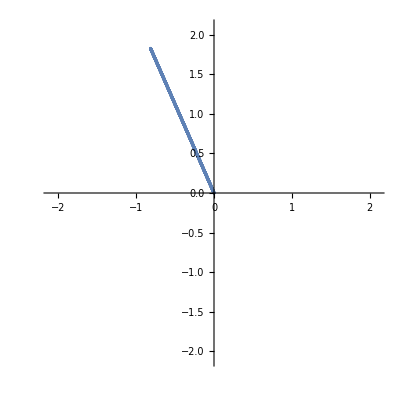

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1;
k=100α;
θ=-α/2;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
(*Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]];*)
```

```mathematica
(*Define the map and its Jacobian*)standardMap[{x_,y_},K_]:=Module[{yn,xn},yn=y+K Sin[x];
xn=Mod[x+yn,2 Pi];
{xn,yn}];

jacobianStandardMap[{x_,y_},K_]:=Module[{dx,dy},dx=1+K Cos[x];
dy=1;
{{dx,dy},{1,1}}];

(*Compute the FTLE*)
Clear[computeFTLE];
computeFTLE[map_,jacobian_,grid_,nSteps_,K_]:=Module[{ftleValues,trajectory,jacobianTrajectory,cumulativeJacobian,singularValues,lambda},(*FTLE computation for each grid point*)ftleValues=ParallelTable[Module[{z0={x,y},z,J,Jcum,singularValueMax},(*Initialize cumulative Jacobian*)Jcum=IdentityMatrix[2];
z=z0;
(*Iterate map and Jacobian*)
Do[J=jacobian[z,K];
Jcum=J.Jcum;(*Accumulate Jacobian product*)z=map[z,K];,{n,1,nSteps}];
(*Compute the largest singular value*)singularValueMax=Max[SingularValueList[Jcum]];
(*FTLE calculation*)lambda=Log[singularValueMax]/nSteps;
lambda],{x,grid[[1,1]],grid[[1,2]],grid[[1,3]]},{y,grid[[2,1]],grid[[2,2]],grid[[2,3]]}];
ftleValues];
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=8.0; (*Parameter for standard map*)
nSteps=2; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=2.0; (*Parameter for standard map*)
nSteps=10; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic]
```

-Graphics-

# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Separating by parity

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

31602

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=25.;
mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
data=husimi[neweigenvec[[2]]];
```

```mathematica
ListDensityPlot[data,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

-Graphics-

```mathematica
d2=ParallelTable[Total[Abs[Conjugate[neweigenvec].i]^4],{i,cohes}];
```

```mathematica
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
```

```mathematica
d2plotn=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>".png",d2plotn]
(*Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plots]*)
```

d2north_J_200_alpha_0.84_k_25..png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvec}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

```mathematica
sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvec=Table[neweigenvec[[i[[1]]]],{i,index}];
sortedeigenval=Table[neweigenval[[i[[1]]]],{i,index}];
```

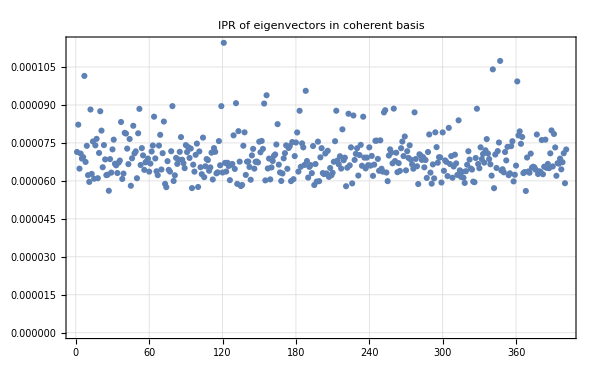

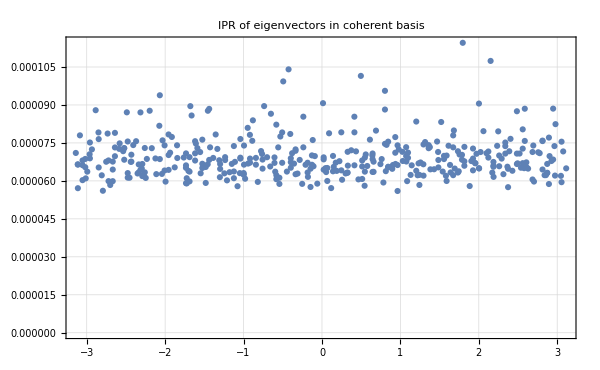

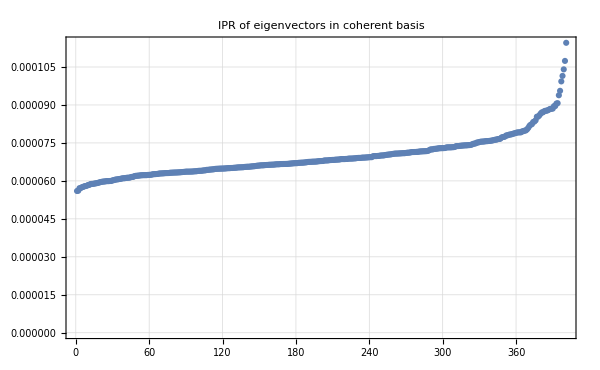

```mathematica
ListPlot[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
```

```mathematica
iprsdicke=ParallelTable[Total[Abs[i]^4],{i,sortedeigenvec}];
```

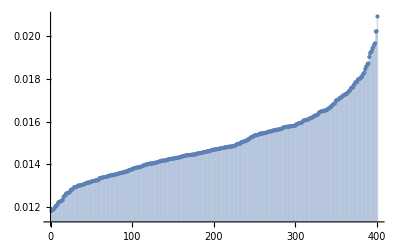

```mathematica
ListPlot[Sort[iprsdicke],PlotRange->All,Filling->Axis]
```

```mathematica
husi1=husimi[sortedeigenvec[[-1]]];
```

```mathematica
ListDensityPlot[husi1,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
```

-Graphics-

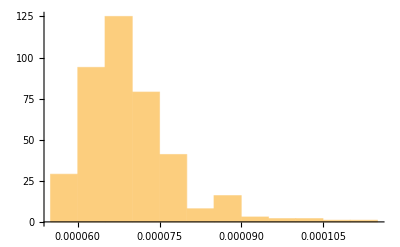

```mathematica
Histogram[iprs,15]
```

```mathematica
Do[

Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[husimi[sortedeigenvec[[i]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,-20,-1,1}]
```

```mathematica
Clear[husimiq];
husimiq[ψ_,q_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^q},{i,Length[region]}]
```

```mathematica
husi3a=husimiq[sortedeigenvec[[-7]],0.1];
husi3b=husimiq[sortedeigenvec[[-7]],0.25];
husi3c=husimiq[sortedeigenvec[[-7]],0.5];
husi3d=husimiq[sortedeigenvec[[-7]],0.99];
husi3e=husimiq[sortedeigenvec[[-7]],2];
husi3f=husimiq[sortedeigenvec[[-7]],4];
husi3g=husimiq[sortedeigenvec[[-7]],8];
```

```mathematica
qlist={0.1,0.25,0.5,0.99,2,4,8};
```

```mathematica
ListDensityPlot[husi3a,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[1]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3b,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[2]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3c,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[3]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3d,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[4]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3e,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[5]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3f,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[6]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListDensityPlot[husi3a,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[1]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3b,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[2]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3c,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[3]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3d,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[4]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3e,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[5]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3f,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta]<>", q = "<>ToString[qlist[[6]]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
ListPlot[{Abs[sortedeigenvec[[1]]]^2,Abs[sortedeigenvec[[-1]]]^2},PlotRange->All,Filling->Axis,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[Abs[sortedeigenvec[[-7]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed"]
```

-Graphics-

## Entanglement entropy

```mathematica
sortedeigenvec//Dimensions
```

{401,401}

```mathematica
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
```

```mathematica
Clear[J,N1,N2];
J=200;
N1=10;
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
b=sortedeigenvec[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[sortedeigenvec]}];
```

```mathematica
Table[Tr[i],{i,rhos}]//ListPlot
```

-Graphics-

```mathematica
info=Table[1-Chop[Tr[i.i]],{i,rhos}];
```

```mathematica
ListPlot[info,PlotLabel->Style["Linear entropy, J1 = 5/2, J2 = 200-5/2",25,Black],PlotTheme->"Detailed",PlotRange->All,ImageSize->600]
ListPlot[Transpose[{Arg[sortedeigenval],info}],PlotLabel->Style["Linear entropy, J1 = 5/2, J2 = 200-5/2",25,Black],PlotTheme->"Detailed",PlotRange->All,ImageSize->600]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[info,PlotLabel->Style["Linear entropy, J1 = 1/2, J2 = 200-1/2",25,Black],PlotTheme->"Detailed",PlotRange->All,ImageSize->600]
ListPlot[Transpose[{Arg[sortedeigenval],info}],PlotLabel->Style["Linear entropy, J1 = 1/2, J2 = 200-1/2",25,Black],PlotTheme->"Detailed",PlotRange->All,ImageSize->600]
```

-Graphics-

-Graphics-

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[plotpuntos,plotsphere,ImageSize->700,PlotLabel->Style["Linear entropy, J1 = 1/2, J2 = 200-1/2",25,Black]]
```

-Graphics3D-

## Random states

```mathematica
random=Table[haar[100],{i,20}];
```

```mathematica
data=Table[husimi[i],{i,random}];
```

```mathematica
Table[ListDensityPlot[i,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]],{i,data}];
```

```mathematica
average=Mean[data];
```

```mathematica
average//Dimensions
```

{14153,3}

```mathematica
Table[Histogram[i[[All,3]]],{i,data}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[average[[All,3]]]
```

-Graphics-

```mathematica
ListDensityPlot[average,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Average Husimi function",25,Black]]
```

-Graphics-

```mathematica
random1=haar[100];
random2=Normalize[Sum[RandomReal[]*i,{i,neweigenvec}]];
random3=Normalize[Sum[Exp[I*RandomReal[{-Pi,Pi}]]*RandomReal[]*i,{i,neweigenvec}]];
```

```mathematica
ListDensityPlot[husimi[random1],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random2],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random3],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

-Graphics-

-Graphics-

-Graphics-

## Scaling

```mathematica
Qs=Table[{Rationalize[i],75/100},{i,0.5,1.0,0.01}];
k=100α;
Qs=(rot[-θ].#&/@Qs);
```

```mathematica
data={};
Do[

cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
cohefloq=ParallelTable[Conjugate[neweigenvec].i,{i,cohes}];
ipr=ParallelTable[Total[Abs[i]^4],{i,cohefloq}];
AppendTo[data,{J,ipr}];

,{J,1,100}];
```

```mathematica
data//Dimensions
```

{100,2}

```mathematica
data[[1]]
```

{1,{0.333577,0.333552,0.33356,0.333603,0.333682,0.333797,0.333949,0.334137,0.334363,0.334627,0.334928,0.335268,0.335646,0.336063,0.336518,0.337011,0.337543,0.338113,0.338721,0.339367,0.34005,0.340769,0.341524,0.342315,0.343141,0.344,0.344892,0.345816,0.346772,0.347756,0.34877,0.34981,0.350876,0.351967,0.353079,0.354213,0.355366,0.356537,0.357722,0.358922,0.360132,0.361352,0.362578,0.36381,0.365044,0.366277,0.367508,0.368734,0.369953,0.371161,0.372356}}

```mathematica
jlist=Range[1,100];
```

```mathematica
newdata=Table[Transpose[{Log[2*i+1],Log[data[[i,2,j]]]}],{j,Length[Qs]},{i,100}];
```

```mathematica
ListPlot[{newdata[[1]],newdata[[25]],newdata[[-1]]},PlotRange->All,Joined->True,PlotTheme->"Detailed", ImageSize->1200]
```

-Graphics-

# Sorting Husimis

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
```

```mathematica
Clear[J];
J=100;
α=2.1;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=100α;
matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];

mats=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;
matM=Table[mats[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mats[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecS=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
d2n=ParallelTable[Total[Abs[Conjugate[neweigenvecN].i]^4],{i,cohes}];
d2s=ParallelTable[Total[Abs[Conjugate[neweigenvecS].i]^4],{i,cohes}];
```

```mathematica
newd2n=Transpose[{region[[All,1]],region[[All,2]],-Log[d2n]/Log[2J+1]}];
newd2s=Transpose[{region[[All,1]],region[[All,2]],-Log[d2s]/Log[2J+1]}];
```

```mathematica
d2plotsn=ListDensityPlot[newd2n,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
d2plotss=ListDensityPlot[newd2s,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["South D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
```

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plotsn]
Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plotss]
```

d2north_J_99_alpha_2.1_k_210._dq_0.025.png

d2south_J_99_alpha_2.1_k_210._dq_0.025.png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvecN}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

```mathematica
sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvecN=Table[neweigenvecN[[i[[1]]]],{i,index}];
```

```mathematica
plot1=ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot2=ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["ϕ",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot3=Histogram[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]}];
```

```mathematica
Export["iprnortha_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot1]
Export["iprnorthb_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot2]
Export["iprnorthc_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot3]
```

iprnortha_J_99_alpha_2.1_k_210._dq_0.025.png

iprnorthb_J_99_alpha_2.1_k_210._dq_0.025.png

iprnorthc_J_99_alpha_2.1_k_210._dq_0.025.png

```mathematica
husi1=husimi[sortedeigenvecN[[1]]];
husi2=husimi[sortedeigenvecN[[-1]]];
```

```mathematica
ListDensityPlot[husi1,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
ListDensityPlot[husi2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
```

-Graphics-

-Graphics-

```mathematica
allhusimissorted=Table[allhusimis[[i[[1]]]],{i,index}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimissorted}];
```

```mathematica
ListDensityPlot[newhusimis[[1]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[newhusimis[[-1]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

-Graphics-

```mathematica
Do[

Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newhusimis[[i]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,2J+1}]
```

```mathematica
NotebookSave[]
```

## <H_0>

```mathematica
k=100α;
(*matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
matn=ConjugateTranspose[rotation2].MatrixPower[Floq[J,α,k,τ],3].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
ope=Sz[J];
```

```mathematica
jzs=ParallelTable[Chop[Conjugate[i].ope.i],{i,neweigenvecN}];
```

```mathematica
ListPlot[Sort[jzs/J],PlotRange->All,ImageSize->500]
```

-Graphics-

```mathematica
ListPlot[Sort[jzs/J],PlotRange->All,ImageSize->500]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[neweigenval],jzs/J}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[neweigenval],jzs/J}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```

-Graphics-

# Comparing similar k values

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=100α;
```

```mathematica
klist=Sort[Table[100α+RandomReal[{-0.05,0.05}],{i,20}]]
```

{83.9536,83.956,83.9609,83.9675,83.9813,83.9816,83.9822,83.9824,83.9832,83.9919,83.9974,83.998,84.004,84.0158,84.0177,84.0215,84.0236,84.0373,84.0484,84.0497}

```mathematica
Do[

k=klist[[q]];
matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];

d2n=ParallelTable[Total[Abs[Conjugate[neweigenvecN].i]^4],{i,cohes}];
newd2n=Transpose[{region[[All,1]],region[[All,2]],-Log[d2n]/Log[2J+1]}];

d2plotsn=ListDensityPlot[newd2n,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",d2plotsn];

allhusimis=Table[husimi[i],{i,neweigenvecN}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];

sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvecN=Table[neweigenvecN[[i[[1]]]],{i,index}];

plot1=ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot2=ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["ϕ",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot3=Histogram[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]}];

Export["iprnortha_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot1];
Export["iprnorthb_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot2];
Export["iprnorthc_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot3];
allhusimissorted=Table[allhusimis[[i[[1]]]],{i,index}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimissorted}];
Do[
Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newhusimis[[i]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]];
,{i,{1,-1}}];



,{q,Length[klist]}]
```